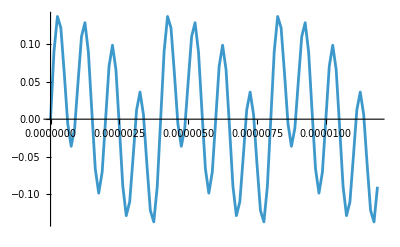

```mathematica
ClearAll["Global`*"];

fs=8000000;
df=500;
n=fs/df;

t=N[Range[0,n-1]/fs];

f1=250000;
f2=500000;
fNoise=1000000;

a1=0.050;
a2=0.025;
aNoise=0.100;

xUseful=a1 Sin[2 Pi f1 t]+a2 Sin[2 Pi f2 t];
xNoise=aNoise Sin[2 Pi fNoise t];
x=xUseful+xNoise;
oneSidedSpectrum[data_,sampleRate_]:=Module[{length,spectrum,amplitude,frequency},length=Length[data];
spectrum=Fourier[data,FourierParameters->{1,-1}];
amplitude=2 Abs[Take[spectrum,length/2+1]];
amplitude[[1]]=amplitude[[1]]/2;
amplitude[[-1]]=amplitude[[-1]]/2;
frequency=Range[0,length/2] sampleRate/length;
Transpose[{frequency,amplitude}]]

samplesShown=Round[12*10^-6 fs];
ListLinePlot[Transpose[{Take[t,samplesShown],Take[x,samplesShown]}]]
```

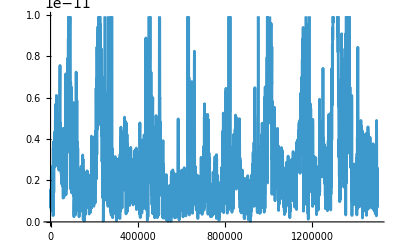

```mathematica
spectrumBefore=Select[oneSidedSpectrum[x,fs],First[#]<=1500000&];
ListLinePlot[spectrumBefore]
```

```mathematica
Manipulate[Module[{filteredSignal,spectrumAfter},filteredSignal=LowpassFilter[x,cutoff,filterLength,SampleRate->fs,Padding->"Periodic"];
spectrumAfter=Select[oneSidedSpectrum[filteredSignal,fs],First[#]<=1500000&];
ListLinePlot[{spectrumBefore,spectrumAfter}]],{{cutoff,700000,"截止频率/Hz"},550000,900000,10000},{{filterLength,201,"FIR长度"},51,401,10}]
```

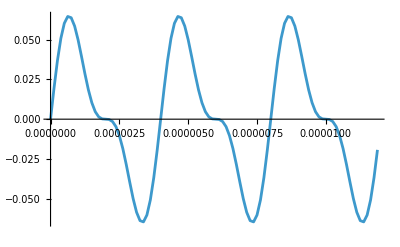

```mathematica
hardCutoff=1000000;
fullSpectrum=Fourier[x,FourierParameters->{1,-1}];
signedFrequency=Join[Range[0,n/2-1],Range[-n/2,-1]] fs/n;
hardMask=Map[If[#<hardCutoff,1,0]&,Abs[signedFrequency]];
hardSpectrum=fullSpectrum hardMask;
xReconstructed=Chop[Re[InverseFourier[hardSpectrum,FourierParameters->{1,-1}]]];
ListLinePlot[Transpose[{Take[t,samplesShown],Take[xReconstructed,samplesShown]}]]
```